```mathematica
Power Plant Investment Simulations
Miles, Duy, RJ

Notes: To initialize all functions (does not execute/load): Evaluation -> Evaluate Initialization Cells

Timing on dual core i5:
	Benevolent Dictator:		  667.124016 s
	Regulated Monopolist:	  466.112730 s
	Triopoly			1645.132342 s
```

```mathematica
Configuration
```

```mathematica
Load previous results
```

```mathematica
benevolentDictator=ReadIt["benevolentDictator.dat"];
regulatedMonopolist=ReadIt["regulatedMonopolist.dat"];
investorCompetition=ReadIt["investorCompetition.dat"];
```

```mathematica
GA Settings
```

```mathematica
populationSize=100;
rounds=200;
rho=0.03;
investors=3;
```

```mathematica
Market Simulation Settings
```

```mathematica
(* Main *)
periods=63;
phases=4;

(* fixed parameters *)
a={300,420,600,360}; (* # of vals must == # phases *)
b=1.0;
i=0.02;

(* maximum production capacity *)
Kr=400;
Ks=50;

(* minimum output *)
Mr=2*Kr/3;
Ms=0;

(* fixed operating cost *)
Fr=5000;
Fs=20;

(* variable operating cost *)
Cr=10;
Dr=0.25;
Cs=150;
Ds=1;
```

```mathematica
System Functions
```

```mathematica
Demand
```

```mathematica
(* Find demand price from quantity;
	t: period,
	z: phase,
	q: quantity *)
InverseDemand[t_,z_,q_]:=a[[z]]*(1+i)^t-b*q;


(* Find demand quantity from price;
	t: period,
	z: phase,
	p: price *)
Demand[t_,z_,p_]:=(a[[z]]*(1+i)^t-p)/b;
```

```mathematica
Supply
```

```mathematica
(* Find supply price from quantity;
	numR: # of type R plants,
	numS: # of type S plants,
	q: quantity *)
InverseSupply[numR_,numS_,q_]:=Piecewise[{
{Cr+ZeroDivide[Dr,numR]*q,numR*Mr≤q≤numR*Kr},
{Cs+(Ds/numS)*(q-numR*Kr),numR*Kr<q≤numR*Kr+numS*Ks}
}];


(* Find supply quantity from price;
	numR: # of type R plants,
	numS: # of type S plants,
	q: quantity *)
Supply[numR_,numS_,p_]:=Piecewise[{
{numR*Mr,0≤p≤Cr+Dr*Mr},
{(p-Cr)*(numR/Dr),Cr+Dr*Mr<p≤Cr+Dr*Kr},
{numR*Kr,Cr+Dr*Kr<p≤Cs},
{numR*Kr+(p-Cs)*(numS/Ds),Cs<p≤Cs+Ds*Ks},
{numR*Kr+numS*Ks,Cs+Ds*Ks<p≤Infinity}
}];
```

```mathematica
Quantity/Price Equilibrium
```

```mathematica
(* Find equilibrium price, given period/phase and plants;
	t: period,
	z: phase,
	numR: # of type R plants,
	numS: # of type S plants *)
Clear[x];
CurrentPrice[t_,z_,numR_,numS_]:=
CurrentPrice[t,z,numR,numS]=Block[{v},
v=x/.Flatten@NSolve[Supply[numR,numS,x]==Demand[t,z,x],x];
If[NumberQ[v],Return[v],Return[0]];
];


(* Find equilibrium quantity, given period/phase and plants;
	t: period,
	z: phase,
	numR: # of type R plants,
	numS: # of type S plants *)
Clear[x];
CurrentQuantity[t_,z_,numR_,numS_]:=
CurrentQuantity[t,z,numR,numS]=Block[{
cp=CurrentPrice[t,z,numR,numS]
},
N@Max[Mr*numR,Demand[t,z,cp]]
];
```

```mathematica
System Cost/Value
```

```mathematica
(* Total value of all units supplied to consumers at given quantity;
	t: period,
	z: phase,
	q: quantity *)
TotalValue[t_,z_,q_]:=q*a[[z]]*(1+i)^t-(b*q^2)/2;


(* Total cost of all units supplied to consumers at given quantity;
	numR: # of type R plants,
	numS: # of type S plants,
	q: quantity *)
TotalCost[numR_,numS_,q_]:=
TotalCost[numR,numS,q]=Piecewise[{
{Cr*q+((Dr/numR)*q^2)/2,numR*Mr≤q≤numR*Kr},
{Cr*numR*Kr+(Dr*numR*Kr^2)/2+Cs*(q-numR*Kr)+((Ds/numS)*(q-numR*Kr)^2)/2,numR*Kr<q≤numR*Kr+numS*Ks}
}]+(numR*Fr+numS*Fs);
```

```mathematica
Profit/Welfare
```

```mathematica
(* Find total profit of system given period/phase & plants;
	t: period,
	z: phase,
	numR: # of type R plants,
	numS: # of type S plants *)
Profit[t_,z_,numR_,numS_]:=
Profit[t,z,numR,numS]=Block[{cp,cq},
If[numR==0&&numS==0,Return[0]];
cp=CurrentPrice[t,z,numR,numS];
cp=If[NumberQ[cp],cp,0];
cq=CurrentQuantity[t,z,numR,numS];
cq=If[NumberQ[cq],cq,0];
cp*cq-TotalCost[numR,numS,cq]
];


(* Find profit for investor in system given period/phase & plants;
	t: period,
	z: phase,
	numR: # of type R plants,
	numS: # of type S plants,
	percentR: % of R plants controlled by investor,
	percentS: % of S plants controlled by investor *)
InvestorProfit[t_,z_,numR_,numS_,percentR_,percentS_]:=
InvestorProfit[t,z,numR,numS,percentR,percentS]=Block[{cp,q,r},
If[numR==0&&numS==0,Return[0]];
cp=CurrentPrice[t,z,numR,numS];
cp=If[NumberQ[cp],cp,0];
q=CurrentQuantity[t,z,numR,numS];
q=If[NumberQ[q],q,0];
r=Piecewise[{
{percentR*(cp*(numR+numS)-TotalCost[numR,numS,Demand[t,z,q]]),numR*Mr≤q≤numR*Kr},
{percentR*(cp*numR*Kr)+percentS*(cp*(q-numR*Kr))-percentS*(Cr*numR*Kr+(Dr*numR*Kr^2)/2)-percentS*(Cs*(q-numR*Kr)+((Ds/numS)*(q-numR*Kr)^2)/2),numR*Kr<q≤numR*Kr+numS*Ks}
},0.];
Return[r];
];


(* Find total social surplus of system given period/phase & plants;
	t: period,
	z: phase,
	numR: # of type R plants,
	numS: # of type S plants *)
Welfare[t_,z_,numR_,numS_]:=
Welfare[t,z,numR,numS]=Block[{cq},
If[numR==0&&numS==0,Return[0]];
cq=CurrentQuantity[t,z,numR,numS];
cq=If[NumberQ[cq],cq,0];
TotalValue[t,z,cq]-TotalCost[numR,numS,cq]
];
```

```mathematica
Lifetime Profits/Welfare
```

```mathematica
(* All functions take a build plan scaffold as input.
Build plan scaffolds take the form:
{
{n1,n2,...,nR}, length = max # plants type R, 0 ≤ nR ≤ # of periods;
{n1,n2,...,nS}, length = max # plants type S, 0 ≤ nS ≤ # of periods;
f (fitness value)
}
*)
```

```mathematica
(* Calculate lifetime social welfare given a build plan; memoized;
	buildPlan: build plan scaffold for simulation lifetime *)
TotalWelfare[buildPlan_]:=TotalWelfare[buildPlan]=Block[{
cbp=ChronoBuildPlan[buildPlan]
},
Total[
Parallelize[
MapIndexed[
(Total[Table[Welfare[#2[[1]],p,#1[[1]],#1[[2]]],{p,1,phases}]]&),
cbp
]
]
]
];


(* Calculate lifetime profit given a build plan; memoized;
	buildPlan: build plan scaffold for simulation lifetime *)
TotalProfit[buildPlan_]:=TotalProfit[buildPlan]=Block[{
cbp=ChronoBuildPlan[buildPlan]
},
Total[
Parallelize[
MapIndexed[
(Total[Table[Profit[#2[[1]],p,#1[[1]],#1[[2]]],{p,1,phases}]]&),
cbp
]
]
]
];


(* Calculate lifetime profit for single investor given its
	ownership percentage and a system build plan;
	systemBuildPlan: chrono build plan of whole system,
	profitShares: table of ownership % per period *)
TotalInvestorProfit[systemBuildPlan_,profitShares_]:=
TotalInvestorProfit[systemBuildPlan,profitShares]=
Total[
MapIndexed[
(Total[
Table[
InvestorProfit[#2[[1]],p,
#1[[1]],#1[[2]],
profitShares[[#2[[1]],1]],
profitShares[[#2[[1]],2]]],
{p,1,phases}
]
]&),
systemBuildPlan
]
];
```

```mathematica
Market Simulation Functions
```

```mathematica
Formatting
```

```mathematica
(* Format a build plan scaffold into a chronological list,
	length = # of periods, where each element is a 2-tuple, {r,s}, 
		with r/s = # of plants of type built at that period;
	buildPlan: build plan scaffold for simulation lifetime *)
ChronoBuildPlan[buildPlan_]:=Block[{r=0,s=0},
Table[
{
If[MemberQ[buildPlan[[1]],j],r+=1,r],
If[MemberQ[buildPlan[[2]],j],s+=1,s]
}
,{j,1,periods}
]
];
```

```mathematica
Maximum Plants
```

```mathematica
(* Find maximum # of profitable plants of type R & S at given
period/phase. Used as upper bound for simulations;
	t: period,
	z: phase *)
MaxPlantsByProfit[t_,z_]:=Block[{r=1,s=1},
While[Profit[t,z,r,0]>0&&r<t,r+=1];
While[Profit[t,z,0,s]>0&&s<t,s+=1];
{r,s}
];


(* Find maximum # of socially beneficial plants of type R & S at
given period/phase. Used as upper bound for simulations;
	t: period,
	z: phase *)
MaxPlantsByWelfare[t_,z_]:=Block[{r=1,s=1},
While[Welfare[t,z,r,0]>0&&r<t,r+=1];
While[Welfare[t,z,0,s]>0&&s<t,s+=1];
{r,s}
];
```

```mathematica
Mutation
```

```mathematica
(* Draw a random mutation, bounded by 0 and # of periods;
	num: number to mutate around,
	set: list of numbers that drawn number must not equal *)
Draw[num_,set_]:=Block[{
d=-1,
n=If[num==0,1,num]
},

While[d>periods||d<0||MemberQ[set,d],
d=RandomVariate[PoissonDistribution[n]];
(*d=RandomInteger[{1,periods}];*)
];
d
];


(* Mutate list of plants of specific type from build plan;
	plants: list of plants of type R or S *)
MutateListPlants[plants_List,maxPlants_]:=Block[{
set,asd,
mutPlants=plants
},
If[maxPlants< periods,
Do[
set=Select[Union[mutPlants],#>0&]; 
mutPlants[[j]]=If[RandomReal[]<rho,
If[mutPlants[[j]]≠0,
If[RandomReal[]<0.5,
0,
Draw[mutPlants[[j]],set]
],
asd=RandomInteger[{0,periods}];
While[MemberQ[Union[mutPlants],asd],
asd=RandomInteger[{0,periods}];
];
asd
]
,
mutPlants[[j]]
];
,{j,1,Length[mutPlants]}
];
];
mutPlants
];


(* Mutate a build plan holding plants type R and S;
	buildPlan: build plan scaffold *)
MutateBuildPlan[buildPlan_List,maxPlants_]:={
MutateListPlants[buildPlan[[1]],maxPlants[[1]]],
MutateListPlants[buildPlan[[2]],maxPlants[[2]]],
buildPlan[[3]]
};


(* Mutate a population of build plans;
	population: population of build plans,
	maxPlants: max # of plants allowed in system *)
Mutate[population_List,maxPlants_]:=ParallelMap[MutateBuildPlan[#,maxPlants]&,population];
```

```mathematica
Reproduction
```

```mathematica
(* Extract fitness values from population of build plans,
	then shift all values positive, with min most val set to 1 *)
PositiveWeights[population_]:=Block[{
min,
weights=Transpose[population][[3]]
},
min=Min[weights];
If[min≤0,Return[(#+Abs[min]+1.0&)/@weights],Return[weights]];
];


(* Pull one weighted random selected build plan 
	from each investor's set,
	populations: list of populations of build plans *)
SelectedBuildPlans[populations_]:=Table[
RandomChoice[PositiveWeights[populations[[i]]]->populations[[i]]],
{i,1,investors}
];


(* Evaluate population fitness, using FitnessFunction;
	population: a population of build plans,
	FitnessFunction: function that returns a fitness value
	for a build plan *)
Fitness[population_,FitnessFunction_]:=Map[{#[[1]],#[[2]],FitnessFunction[#]}&,population];


(* Evaluate fitness of investor's build plans;
	populations: the set of build plans for each investor,
	selectedBuildPlans: one selected build plan per investor *)
InvestorFitness[populations_,selectedBuildPlans_]:=Block[{sbp,ps},
ParallelTable[
sbp=SystemBuildPlan@ReplacePart[selectedBuildPlans,k->populations[[k,j]]];
ps=ProfitShare[populations[[k,j]],sbp];
ReplacePart[populations[[k,j]],3->TotalInvestorProfit[sbp,ps]]
,{j,1,populationSize},{k,1,investors}
]
];


(* Gladiator-style reproduction, comparing fitness values;
	population: a population of build plans *)
Reproduce[population_]:=Block[{sample},
ParallelTable[
sample=RandomSample[population,2];
If[sample[[1,3]]≥sample[[2,3]],sample[[1]],sample[[2]]],
{populationSize}
]
];
```

```mathematica
Investor Competition Functions
```

```mathematica
(* Return 0 if dividing by zero *)
ZeroDivide[numerator_,denominator_]:=If[denominator==0,0,N[numerator/denominator]];


(* Combine build plans in list into one
	chronological build plan;
	buildPlans: list of build plans to combine *)
SystemBuildPlan[buildPlans_]:=Total[ChronoBuildPlan/@buildPlans];


(* Calculate the profit share of an investors plants R, S;
	investorBuildPlan: build plan scaffold of investor,
	systemBuildPlan: chrono build plan of entire system *)
ProfitShare[investorBuildPlan_,systemBuildPlan_]:=Block[{
cibp=ChronoBuildPlan[investorBuildPlan]
},
Table[
{
ZeroDivide[cibp[[t,1]],systemBuildPlan[[t,1]]],
ZeroDivide[cibp[[t,2]],systemBuildPlan[[t,2]]]
},
{t,1,periods}
]
];
```

```mathematica
Population Random Seeding
```

```mathematica
(* Generates random list with length ≤ n, of 2-tuples
{index,number}, where index = random integer between 0 & n
and numbers = random integer between 0 & m. Used as;
	n: max plants of type allowed,
	m: max periods in simulation *)
RandomPairs[n_,m_]:=Block[{
indices,numbers,
len=RandomInteger[n]
},
indices=RandomSample[Range[1,n],len];
numbers=RandomSample[Range[1,m],len];
Transpose[{indices,numbers}]
];


(* Generate a random build plan, building max of type R/S;
	maxR: max # of plants type R allowed,
	maxS: max # of plants type S allowed *)
RandomBuildPlan[maxR_,maxS_]:=Block[{
r=Table[0,{maxR}],
s=Table[0,{maxS}],
rR=RandomPairs[maxR,periods],
rS=RandomPairs[maxS,periods]
},
Do[r[[rR[[j,1]]]]=rR[[j,2]],{j,1,Length[rR]}];
Do[s[[rS[[j,1]]]]=rS[[j,2]],{j,1,Length[rS]}];
{r,s,0}
];


(* Generate a random population of build plans;
	maxR: max # of plants type R allowed,
	maxS: max # of plants type S allowed,
	size: size of the population *)
GeneratePopulation[maxR_,maxS_,size_]:=Table[RandomBuildPlan[maxR,maxS],{size}];
```

```mathematica
Simulations
```

```mathematica
Benevolent Dictator
```

```mathematica
(*  Goal: Maximize total social welfare of system *)

(*  1. mutate population bounded by max # plants allowed,
	2. evaluate fitness, calculated by total social welfare
		produced by build plan,
	3. reproduce gladiator-style, comparing fitness value
*)
```

```mathematica
BenevolentDictator:=Block[{
population,
maxPlants=MaxPlantsByWelfare[periods,phases-1]
},

(* Initialize the population *)
population=GeneratePopulation[maxPlants[[1]],maxPlants[[2]],populationSize];

Do[
(* Mutate *)
population=Mutate[population,maxPlants];

(* Fitness *)
population=Fitness[population,TotalWelfare];

(* Reproduce *)
population=Reproduce[population];

(* Rinse & Repeat *)
,{rounds}
];

(* Output population *)
population
];
```

```mathematica
Regulated Monopolist
```

```mathematica
(*  Goal: Maximize total profit of system *)

(*  1. mutate population bounded by max # plants allowed,
	2. evaluate fitness, calculated by total profit
		produced by build plan,
	3. reproduce gladiator-style, comparing fitness value
*)
```

```mathematica
RegulatedMonopolist:=Block[{
population,
maxPlants=MaxPlantsByProfit[periods,phases-1]
},

(* Initialize the population *)
population=GeneratePopulation[maxPlants[[1]],maxPlants[[2]],populationSize];

Do[
(* Mutate *)
population=Mutate[population,maxPlants];

(* Fitness *)
population=Fitness[population,TotalProfit];

(* Reproduce *)
population=Reproduce[population];

(* Rinse & Repeat *)
,{rounds}
];

(* Output population *)
population
];
```

```mathematica
Investor Competition (Triopoly)
```

```mathematica
(*  Goal: Maximize total profit for each investor *)

(*  1. pull off one weighted random selected build plan
		from each investor's build plans,
	2. mutate each investor population,
	3. for each build plan BP in a population
		a. combine with selected build plans from other investors
		b. calculate share of BP
		c. find profit share of BP out of total system profit,
	4. reproduce gladiator-style interally for each investor's build plans
*)
```

```mathematica
InvestorCompetition:=Block[{
populations,(* set of build plans for each investor *)
selectedBuildPlans,
maxPlants=MaxPlantsByProfit[periods,phases-1]
},

(* Initialize the population *)
populations=ParallelTable[
GeneratePopulation[maxPlants[[1]],maxPlants[[2]],populationSize],
{investors}
];

Do[
(* Pull off selected build plans *)
selectedBuildPlans=SelectedBuildPlans[populations];

(* Mutate *)
populations=Mutate[#,maxPlants]&/@populations;

(* Fitness *)
populations=InvestorFitness[populations,selectedBuildPlans];

(* Reproduce *)
populations=Reproduce/@populations;

(* Rinse & Repeat *)
,{rounds}
];

(* Output populations *)
populations
];
```

```mathematica
Execution
```

```mathematica
Run Simulations
```

```mathematica
benevolentDictator=BenevolentDictator;//AbsoluteTiming
```

{904.72699,Null}

```mathematica
regulatedMonopolist=RegulatedMonopolist;//AbsoluteTiming
```

{575.03844,Null}

```mathematica
investorCompetition=InvestorCompetition;//AbsoluteTiming
```

$Aborted

```mathematica
Results
```

```mathematica
Text[Style["Benevolent Dictator - Welfare maximizing",20,Bold,Hue[.7,.7,.7]]]
TableForm[SortBy[Tally@Map[Sort,DeleteCases[benevolentDictator,0,Infinity],{-2}],Last]//Reverse,
TableDepth->2,
TableDirections->Column,
TableHeadings->{None,{"Build Plan (R | S)","#"}}
]
Print["\n"];
Text[Style["Regulated Monopolist - Profit maximizing",20,Bold,Hue[.7,.7,.7]]]
TableForm[SortBy[Tally@Map[Sort,DeleteCases[regulatedMonopolist,0,Infinity],{-2}],Last]//Reverse,
TableDepth->2,
TableDirections->Column,
TableHeadings->{None,{"Build Plan (R | S)","#"}}
]
Print["\n"];
Text[Style["Triopoly- 1st player",20,Bold,Hue[.7,.7,.7]]]
TableForm[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[1]],0,Infinity],{-2}],Last]//Reverse,
TableDepth->2,
TableDirections->Column,
TableHeadings->{None,{"Build Plan (R | S)","#"}}
]
Text[Style["Triopoly- 2nd player",20,Bold,Hue[.7,.7,.7]]]
TableForm[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[2]],0,Infinity],{-2}],Last]//Reverse,
TableDepth->2,
TableDirections->Column,
TableHeadings->{None,{"Build Plan (R | S)","#"}}
]
Text[Style["Triopoly- 3rd player",20,Bold,Hue[.7,.7,.7]]]
TableForm[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[3]],0,Infinity],{-2}],Last]//Reverse,
TableDepth->2,
TableDirections->Column,
TableHeadings->{None,{"Build Plan (R | S)","#"}}
]
Print["\n"];
```

Benevolent Dictator - Welfare maximizing

Build Plan (R | S) | #
{{1,12,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30815×10^7} | 63
{{1,9,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30492×10^7} | 4
{{1,12,37,52,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.19825×10^7} | 3
{{1,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.05278×10^7} | 3
{{1,12,31,53,59,63},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.24668×10^7} | 2
{{1,13,37,53,63},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30519×10^7} | 2
{{1,13,37,53,62},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30109×10^7} | 2
{{1,12,37,53,57},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.26018×10^7} | 2
{{1,12,37,46,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.17148×10^7} | 2
{{1,12,27,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.00791×10^7} | 2
{{2,9,41,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.27548×10^7} | 2
{{1,12,37,51},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30548×10^7} | 2
{{1,12,33,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30263×10^7} | 2
{{1,12,37,53,55,59},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.1085×10^7} | 1
{{1,12,37,53,62},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30117×10^7} | 1
{{1,12,37,53,61},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.29581×10^7} | 1
{{1,12,27,33,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},8.92058×10^7} | 1
{{1,12,24,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},8.97786×10^7} | 1
{{1,8,24,53,63},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.22977×10^7} | 1
{{12,37,48,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},8.94278×10^7} | 1
{{1,10,37,53},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.30659×10^7} | 1
{{1,12,37},{1,2,3,4,5,6,7,9,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63},9.27073×10^7} | 1

Regulated Monopolist - Profit maximizing

Build Plan (R | S) | #
{{1},{1,23,24,25,52},3.67997×10^7} | 86
{{1,62},{1,23,24,25,52},3.61638×10^7} | 2
{{1,56},{1,23,24,25,52},3.40769×10^7} | 2
{{1,46},{1,23,24,25,52},3.07597×10^7} | 2
{{13,32,56},{1,23,24,25,52},2.21192×10^7} | 1
{{1,57},{1,23,24,25,52},3.44558×10^7} | 1
{{1,53},{1,23,24,25,52},3.29881×10^7} | 1
{{1,34},{1,23,24,25,52},2.71644×10^7} | 1
{{1,26},{1,23,24,25,52},2.51392×10^7} | 1
{{1,22},{1,23,24,25,52},2.41756×10^7} | 1
{{1,16},{1,23,24,25,52},2.26287×10^7} | 1
{{2},{1,23,24,25,52},3.67883×10^7} | 1

Triopoly- 1st player

Build Plan (R | S) | #
{{3},{2,4,5,16,18,19,23,27,33,35,39,44,45,53,59},97961.9} | 50

Triopoly- 2nd player

Build Plan (R | S) | #
{{3},{2,4,5,16,18,19,23,27,33,35,39,44,45,53,59},97961.9} | 50

Triopoly- 3rd player

Build Plan (R | S) | #
{{3},{2,4,5,16,18,19,23,27,33,35,39,44,45,53,59},97961.9} | 50

```mathematica
Pretty Graphs
```

```mathematica
Benevolent Dictator
```

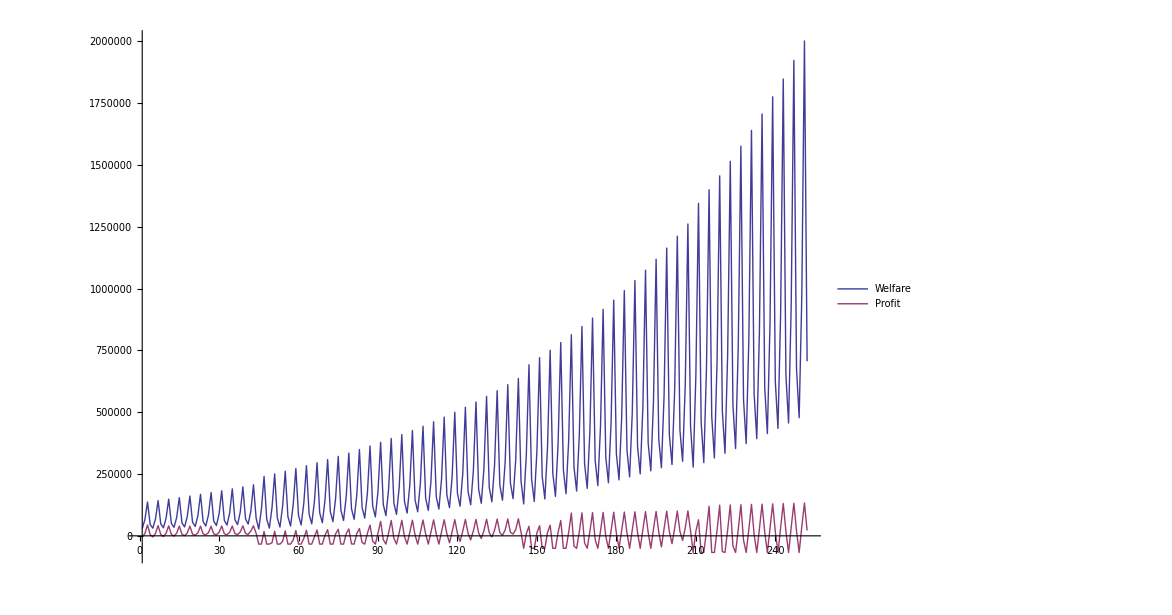

```mathematica
bdtallied=Reverse[SortBy[Tally@Map[Sort,DeleteCases[benevolentDictator,0,Infinity],{-2}],Last]][[All,1]];
bp=ChronoBuildPlan/@bdtallied;
out=Flatten@Table[Welfare[j,k,bp[[1,j,1]],bp[[1,j,2]]],{j,1,periods},{k,1,phases}];
plotMax=Max[out];
(*outasd=Flatten@Table[Welfare[j,k,bp[[2,j,1]],bp[[2,j,2]]],{j,1,periods},{k,1,phases}];*)
outprof=Flatten@Table[Profit[j,k,bp[[1,j,1]],bp[[1,j,2]]],{j,1,periods},{k,1,phases}];
ListLinePlot[{out,outprof}, PlotRange->All,PlotLegends->{"Welfare","Profit"}]
```

```mathematica
Regulated Monopolist
```

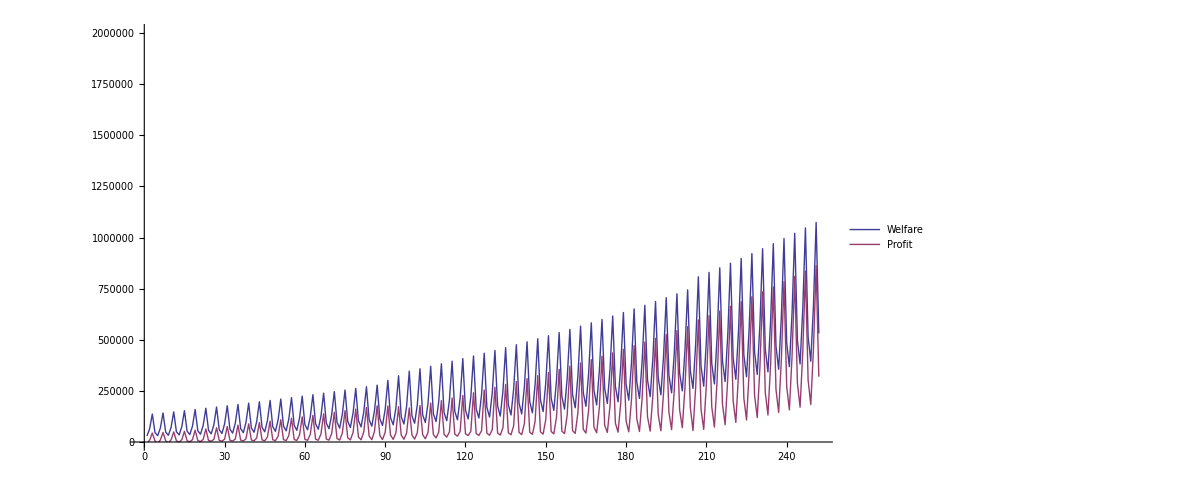

```mathematica
rmtallied=Reverse[SortBy[Tally@Map[Sort,DeleteCases[regulatedMonopolist,0,Infinity],{-2}],Last]][[All,1]];
bp2=ChronoBuildPlan/@rmtallied;
out2=Flatten@Table[Profit[j,k,bp2[[1,j,1]],bp2[[1,j,2]]],{j,1,periods},{k,1,phases}];
out2welf=Flatten@Table[Welfare[j,k,bp2[[1,j,1]],bp2[[1,j,2]]],{j,1,periods},{k,1,phases}];
ListLinePlot[{out2welf,out2},PlotRange->{0,plotMax},PlotLegends->{"Welfare","Profit"}]
```

```mathematica
Investor Competition
```

```mathematica
ic1=ChronoBuildPlan/@Reverse[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[1]],0,Infinity],{-2}],Last]][[All,1]];
ic2=ChronoBuildPlan/@Reverse[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[2]],0,Infinity],{-2}],Last]][[All,1]];
ic3=ChronoBuildPlan/@everse[SortBy[Tally@Map[Sort,DeleteCases[investorCompetition[[3]],0,Infinity],{-2}],Last]][[All,1]];
icout1=Flatten@Table[Profit[j,k,ic1[[1,j,1]],ic1[[1,j,2]]],{j,1,periods},{k,1,phases}];
icout2=Flatten@Table[Profit[j,k,ic2[[1,j,1]],ic2[[1,j,2]]],{j,1,periods},{k,1,phases}];
icout3=Flatten@Table[Profit[j,k,ic3[[1,j,1]],ic3[[1,j,2]]],{j,1,periods},{k,1,phases}];
sbpo=SystemBuildPlan[{investorCompetition[[1,1]],investorCompetition[[2,1]],investorCompetition[[3,1]]}];
systemwelfare=Flatten@Table[Welfare[j,k,sbpo[[j,1]],sbpo[[j,2]]],{j,1,periods},{k,1,phases}];
ListLinePlot[{icout1,icout2,icout3,systemwelfare},PlotRange->All,PlotLegends->{"Profit 1","Profit 2","Profit 3","System Welfare"}]
```

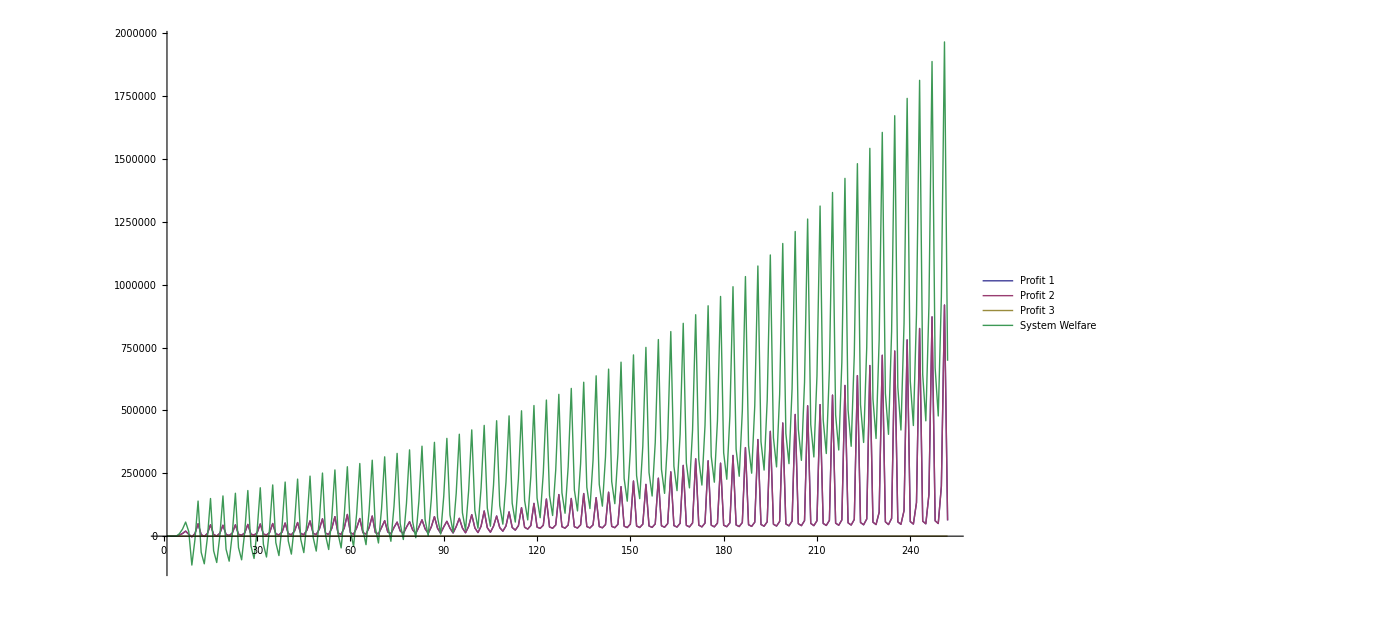

```mathematica
Save/Load
```

```mathematica
(* saves to notebook directory *)
SaveIt[varnamestring_]:=Module[{output},output=Export[NotebookDirectory[]<>varnamestring<>".dat",ToString[ToExpression[varnamestring]//InputForm],"String"];
ClearMemory;
output];

SaveIt[filename_,expr_]:=Module[{output},output=Export[filename<>".dat",ToString[expr//InputForm],"String"];
ClearMemory;
output];

(* retrieves from notebook directory *)
ReadIt[filename_]:=Module[{output},output=ToExpression[Import[NotebookDirectory[]<>StringReplace[filename,".dat"->""]<>".dat","String"]];
ClearMemory;
output];
```

```mathematica
SaveIt["benevolentDictator"];
SaveIt["regulatedMonopolist"];
SaveIt["investorCompetition"];
```